```mathematica
SetDirectory[NotebookDirectory[]];

tA[]:=(CasZ=SessionTime[];DateZ=DateString[{ "Start ","Time", " ","DayName", " ","Day", "/","Month"}];Date1=Date[];);
tB[]:=(CasK=SessionTime[];DateK=DateString[{ "Konec ","Time", " ","DayName", " ","Day", "/","Month"}];Date2=Date[];
Print[DateString[Date2-Date1,{ "TIME"," ","Time"," ","Day"}]<>"  #  "<>DateZ<>" / "<>DateK];);
```

# Methods for chaos detection :

## 1. Box-counting method

```mathematica
BoxCount[list_,delta0_,scale_,min_]:=  
Block[{tmp,delta,nmax,l,i},tmp={};

delta=delta0;
nmax=Abs[Ceiling[Log[min/delta0]/Log[scale]]];

Do[
{
l=Length[Complement[Ceiling[list/delta],tmp]];
AppendTo[tmp,{delta,l}];
delta=delta* scale
},
{i,1,nmax}];

Return[tmp]];  
odhadDimenze[{x_,y_}]:=N[{-Log[10,x],Log[10,y]}]; 

BoxCount1[dataa_]:=(
Clear[x,EHM,EHM0,EHM1,EHM2,EHM3,n2,n1];

EHM =BoxCount[(dataa/Max[dataa])+0.,1.0,0.5,0.001];
EHM1=Map[odhadDimenze,EHM];
EHM1;
EHM2 = Fit[Take[EHM1,Take[Length[EHM1]]],{1,x},x];
EHM2;
If[Length[EHM2]<1,0,
EHM3 = Take[EHM2,-1]/x;
EHM3 ]
);
```

```mathematica
(*BoxCount1[dataa_]:=(
Clear[x,EHM,EHM5,EHM1,EHM2,EHM3,n,n1];
Module[{n,EHM1,EHM2,EHM3,EHM4,EHM5},
dataaa=  EMB3[dataa];
EHM =BoxCount[dataaa,1.0,0.5,0.0000000000001];

EHM1=Map[odhadDimenze,EHM];
EHM1;
n=1;
While[EHM1[[n]][[2]]  ≠  EHM1[[n+1]][[2]],n ;n++];
EHM5= Take[EHM1,n-1];
EHM2 = Fit[Take[EHM5,Take[Length[EHM5]]],{1,x},x];
EHM2;
If[Length[EHM2]<1,0,
EHM3 = Take[EHM2,-1]/x;
EHM3 ]]
);*)
```

## 2. Correlation dimension -D2

```mathematica
corrDIMdim[DData_] := (
Clear[my,x,CDIM,fit,r,nF,i];
my=Log[10,N[Module[{nF=Nearest[DData->Automatic]},Table[{r,Tr[Table[Tr[UnitStep[nF[DData[[i]],{All,r}]-i-1]],{i,1,Length[DData]}]]},{r,0.001,0.011,0.001}]]]];
fit=Fit[my,{1,x},x];

If[Length[fit]<1,0,
CDIM = Take[fit,-1]/x;
CDIM  ]

);
```

```mathematica
er[dat_]:=  
(ST =StandardDeviation[dat];
cor[min_,max_,fac_]:=  
min*( fac ^Range[Floor[Log[ max/ min] / Log[fac]]]);
cor[0.1*ST,0.5*ST,1.03])

 (*data={Drop[dataa,-1],Drop[dataa,1]}ᵀ;
data={Drop[dataa,-2],Take[dataa,{2,-2}],Drop[dataa,2]}ᵀ;*)

EMB1[dataa_]:=(
data={Drop[dataa,-1],Drop[dataa,1]}ᵀ
);


EMB3[data_]:={Drop[data,-2],Take[data,{2,-2}],Drop[data,2]}ᵀ;





 (* corrDIMdim1[dataa_]:=(
correlationSum[data_,τ_,mMax_,minΔt_Integer?(#≥1&),minExp_,maxExp_,nExp_]:=
Table[Module[{emb,nn,ed,bin,di},
emb=ParallelTable[Take[data,{i,i+τ(m-1),τ}],{i,Length[data]-τ(m-1)}];
nn=Length[emb];
ed=Flatten[ParallelTable[di=emb⟦i⟧;
EuclideanDistance[di,#]&/@Take[emb,{i+minΔt,nn}],{i,nn-minΔt}]];
bin=N@Binomial[nn-minΔt+1,2];
{10.^#,Total[UnitStep[(10.^#)-ed]]/bin}&/@Range[minExp,maxExp,(maxExp-minExp)/(nExp-1)]],
{m,mMax}];
fit = Fit[Flatten[Log[correlationSum[dataa,1,1,1,-3,0.1,11]],1],{1,x},x];
If[Length[fit]==0,0,fit[[2]]/x]
);*)
```

```mathematica
corrDIMdim1[dataa_]:=(
correlationSum[data_,τ_,mMax_,minΔt_Integer?(#≥1&),minExp_,maxExp_,nExp_]:=
Table[Module[{emb,nn,ed,bin,di},
emb=Table[Take[data,{i,i+τ(m-1),τ}],{i,Length[data]-τ(m-1)}];
nn=Length[emb];
ed=Flatten[Table[di=emb⟦i⟧;
EuclideanDistance[di,#]&/@Take[emb,{i+minΔt,nn}],{i,nn-minΔt}]];
bin=N@Binomial[nn-minΔt+1,2];
{10.^#,Total[UnitStep[(10.^#)-ed]]/bin}&/@Range[minExp,maxExp,(maxExp-minExp)/(nExp-1)]],
{m,mMax}];
fit = Fit[Flatten[Log[correlationSum[dataa,1,1,1,-3,0.1,11]],1],{1,x},x];
If[Length[fit]==0,0,fit[[2]]/x]);
```

```mathematica
(* corrDIMdim1[dataa_,em_,dtim_]:=(
correlationSum[data_,τ_,mMax_,minΔt_Integer?(#≥1&),minExp_,maxExp_,nExp_]:=
Table[Module[{emb,nn,ed,bin,di},
emb=Table[Take[data,{i,i+τ(m-1),τ}],{i,Length[data]-τ(m-1)}];
nn=Length[emb];
ed=Flatten[Table[di=emb⟦i⟧;
EuclideanDistance[di,#]&/@Take[emb,{i+minΔt,nn}],{i,nn-minΔt}]];
bin=N@Binomial[nn-minΔt+1,2];
{10.^#,Total[UnitStep[(10.^#)-ed]]/bin}&/@Range[minExp,maxExp,(maxExp-minExp)/(nExp-1)]],
{m,mMax}];
fit = Fit[DeleteCases[Log10[correlationSum[dataa,dtim,em,1,-3,0.1,11][[em]]],{_,Indeterminate}],{1,x},x];
If[Length[fit]==0,0,fit[[2]]/x]
);*)
```

```mathematica
falseNearestNeighbors[data_,τ_,mMax_,T1_,T2_]:=Module[{emb,m,n,σ,count,nf,x,yPos,y,Rm,incr},
emb=Table[Table[Take[data,{i,i+τ(m-1),τ}],{i,Length[data]-τ(m-1)}],{m,mMax+1}];
n=Length/@emb;
σ=StandardDeviation[data];
Table[count=0;
nf=Nearest[emb⟦m⟧->Range[n⟦m⟧]];
Do[x=emb⟦m,i⟧;
yPos=Last[nf[x,2]];
If[yPos≤n⟦m⟧-τ,y=emb⟦m,yPos⟧,Continue[]];
Rm=EuclideanDistance[x,y];
incr=Abs[Last[emb⟦m+1,i⟧]-Last[emb⟦m+1,yPos⟧]];
Quiet@If[incr/Rm>T1||incr/σ>T2,count=count+1],{i,n⟦m+1⟧}];
{m,N[count/n⟦m+1⟧]},{m,mMax}]]


corrDIMdim1[dataa_]:=(
correlationSum[data_,τ_,mMax_,minΔt_Integer?(#≥1&),minExp_,maxExp_,nExp_]:=
Table[Module[{emb,nn,ed,bin,di},
emb=Table[Take[data,{i,i+τ(m-1),τ}],{i,Length[data]-τ(m-1)}];
nn=Length[emb];
ed=Flatten[Table[di=emb⟦i⟧;
EuclideanDistance[di,#]&/@Take[emb,{i+minΔt,nn}],{i,nn-minΔt}]];
bin=N@Binomial[nn-minΔt+1,2];
{10.^#,Total[UnitStep[(10.^#)-ed]]/bin}&/@Range[minExp,maxExp,(maxExp-minExp)/(nExp-1)]],
{m,mMax}];

n=1;
While[falseNearestNeighbors[dataa,1,5,15,2][[n]][[2]]≠0 &&n<5,n;n++];
fit = Fit[DeleteCases[Log10[correlationSum[dataa,1,n,20,-3,0.5,18][[n]]],{_,Indeterminate}],{1,x},x];
If[Length[fit]==0,0,fit[[2]]/x]
);
```

```mathematica
(*averageMutualInformation[data_,τMax_,binWidth_]:=Module[{iter,n=Length[data],pi,pij},
ParallelTable[iter={Min[data],Max[data]+binWidth,binWidth};
pi=N[BinCounts[data,iter]/n];
pij=N[BinCounts[{Drop[data,-τ],Drop[data,τ]}ᵀ,iter,iter]/(n-τ)];
{τ,Total[DeleteCases[Flatten[pij Log2[pij/KroneckerProduct[pi,pi]]],Indeterminate|∞]]},{τ,0,τMax}]]*)

(*corrDIMdim1[data_]:=
(
dataa =  EMB3[data];
m=Table[{r,Total[Table[Length[Drop[Nearest[Drop[dataa,i-1],dataa[[i]],{All,r}],1]],{i,1,Length[dataa]}]]},{r,er[data]}];
fit=Fit[Log[10,m],{1,x},x];
If[Length[fit]<1,0,
CDIM = Take[fit,-1]/x;
CDIM  ]);*)
```

```mathematica
corrDIMdim1[data_]:=
(dataaa=  data/ Max[data];
dataa =  EMB3[dataaa];
(m=Table[{r,Total[Table[Length[Drop[Nearest[Drop[dataa,i-1],dataa[[i]],{All,r}],1]],{i,1,Length[dataa]}]]},{r,0.001,0.011,0.001}];
fit=Fit[Log[10,m],{1,x},x];

If[Length[fit]<1,0,
CDIM = Take[fit,-1]/x;
CDIM  ]));
```

```mathematica
corrDIMdim1[data_]:=
(dataaa= data/ Max[data];
dataa =  EMB3[dataaa];
(m=Table[{r,Total[Table[Length[Drop[Nearest[Drop[dataa,i-1],dataa[[i]],{All,r}],1]],{i,1,Length[dataa]}]]},{r,0.001,0.011,0.001}];

m=DeleteCases[m,{_,0}];

fit=Fit[Log[10,m],{1,x},x];

If[Length[fit]<1,0,
CDIM = Take[fit,-1]/x;
CDIM  ]));
```

## 3. Lyapunov exponent λ

```mathematica
Lyapun1[dataa_]:=( 
Clear[x,EHM,EHM0,EHM1,EHM2,EHM3,n2,n1,DaTA];
Lya[data_,τ_,mMax_,ϵ_,δMax_,h_]:=
Table[Module[{emb,nn,nf,neigh},
emb=Table[Take[data,{i,i+τ(m-1),τ}],{i,Length[data]-τ(m-1)}];
nn=Length[emb];
nf=Nearest[emb->Range[nn]];
neigh=Table[DeleteCases[Rest[nf[emb⟦t⟧,{∞,ϵ}]],p_/;p>nn-δMax],{t,nn-δMax}];
Table[{δ,Mean[DeleteCases[
Table[If[Length[neigh⟦t⟧]==0,"d",
Log[Mean[Abs[data⟦t+(m-1)τ+δ⟧-data⟦neigh⟦t⟧+(m-1)τ+δ⟧]]]],
{t,nn-δMax}],"d"|Indeterminate]]},
{δ,0,δMax}]],{m,mMax}];
s = Lya[dataa,1,1,0.001,20,1];
ll=Fit[s[[1]],{1,x},x][[2]]/x
);
```

```mathematica
Lyapun2[dataa_]:=(
Lya[data_,τ_,mMax_,ϵ_,δMax_,h_]:=
Table[Module[{emb,nn,nf,neigh},
emb=Table[Take[data,{i,i+τ(m-1),τ}],{i,Length[data]-τ(m-1)}];
nn=Length[emb];
nf=Nearest[emb->Range[nn]];
neigh=Table[DeleteCases[Rest[nf[emb⟦t⟧,{∞,ϵ}]],p_/;p>nn-δMax],{t,nn-δMax}];
SMT1 =Table[{δ,SMT2 =Mean[ SMT3=DeleteCases[
SMT4 =Table[If[Length[neigh⟦t⟧]==0,"d",
Log[Mean[Abs[data⟦t+(m-1)τ+δ⟧-data⟦neigh⟦t⟧+(m-1)τ+δ⟧]]]],
{t,nn-δMax}],"d"|Indeterminate]]},
{δ,0,δMax}]],{m,mMax}];
s = Lya[dataa,1,1,0.001,20,1];
ll=Fit[s[[1]],{1,x},x][[2]]/x;
If[Length[ll]>1,
n=1;While[
IntervalMemberQ[Interval[{-Infinity,Infinity}],SMT1[[n]][[2]]],Take[SMT1[[n]]];n++];
n;
If[n==1,0,lll=Fit[Take[s[[1]],n-1],{1,x},x][[2]]/x],ll]
 );
```

## Lyapunov exponent analytically

```mathematica
λ[r_]:=Module[{f,l},f[x_]:=r x (1-x);
l[x_]:=Log[Abs[r (1-2 x)]];
Mean[l[NestList[f,0.1,1*^2]]]];
pick=Plot[λ[r],{r,2,4},PlotStyle->{Thickness[.007],Black},AxesLabel->{"r","λ(r)"}];

picL=Show[{figX,pick},AspectRatio->1,PlotRange->{{2,4},{-3,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Max. Lyapunov exponent  λ_m"}];
```

## 4. RQA

```mathematica
f1=Compile[{{n,_Real,1}},(Count[Flatten[UnitStep[0.01*Sqrt[Variance[n]]-Table[Sqrt[Abs[(n[[i]]-n[[j]])^2]],{i,1,Length[n]},{j,1,Length[n]}]]],1]-(Length[n]+1))/(Length[n]^2),CompilationTarget->"C",RuntimeAttributes->Listable,RuntimeOptions->"Speed"]

ClearAll[RpRR];
RpRR[data_]:=Module[{rr,N1,idx,R,SR,RR,DDE,DET,i,j,DE},rr=0.01*Sqrt[Variance[data]];
N1=Length[data];
R=ConstantArray[0,{N1,N1}];
idx=Nearest[data->Automatic,data,{∞,rr}][[All,2;;]];
MapIndexed[{x,y}↦R[[y,x]]=1,idx];
R;
SR =Total[Total[R]];
RR=SR/(N1^2);
N[{RR}]
]

ClearAll[Rp1];
Rp1[data_]:=Module[{rr,N1,idx,R,SR,RR,DDE,DET,i,j,DE},rr=0.01*Sqrt[Variance[data]];
N1=Length[data];
R=ConstantArray[0,{N1,N1}];
idx=Nearest[data->Automatic,data,{∞,rr}][[All,2;;]];
MapIndexed[{x,y}↦R[[y,x]]=1,idx];
R;
SR =Total[Total[R]];
RR=SR/(N1^2);
oneCount[list_,len_]:=Total@UnitStep[ListCorrelate[ArrayPad[ConstantArray[1,len],1,-1],list,{2,-2},0]-len];
DE =Total[Table[oneCount[Diagonal[R,i],1],{i,1,Length[Diagonal[R,1]]}]] ;
DET =(SR-2*DE )/SR;
N[{RR,DET}]
]

ClearAll[Rp3];
Rp3[data_]:=Module[{rr,N1,idx,R,SR,RR,DDE,DET,i,j,ENTR,pp,F,L,l},rr=0.01*Sqrt[Variance[data]];
N1=Length[data];
R=ConstantArray[0,{N1,N1}];
idx=Nearest[data->Automatic,data,{∞,rr}][[All,2;;]];
MapIndexed[{x,y}↦R[[y,x]]=1,idx];
R;

Smat[Mat_]:=(
oneCount[list_,len_]:=Total@UnitStep[ListCorrelate[ArrayPad[ConstantArray[1,len],1,-1],list,{2,-2},0]-len];
oo =Table[Table[oneCount[Diagonal[Mat,j],i],{i,1,Length[Diagonal[Mat,j]]}],{j,1,Length[Mat]-1}];
Yout =Total@Table[Flatten[{oo[[i]],Table[0,{i-1}]}],{i,Length[oo]}]
);
Yout=Smat[R];
S=2*Yout;
SR=0;
For[i=1,i<N1,i++,  
           SR=SR+i*S[[i]];];
RR=SR/(N1^2);
Lmin=2;
If[SR==0,
DET=0,
DET=(SR-Sum[S[[i]],{i,Lmin-1}])/SR;];

pp=S/Sum[S[[i]],{i,Length[S]}];
entropy=0;
F =Complement[Table[{i},{i,Lmin,Length[S]}],Position[S,0]];
l = Length[F];

If[l==0,ENTR=0,ENT = Table[pp[[F[[i]]]]*Log[pp[[F[[i]]]]],{i,1,Length[F]}];
ENTR = - Sum[ENT[[i]],{i,1,Length[ENT]}]
];
L =(SR-S[[1]])/Sum[S[[i]],{i,Lmin,Length[S]}];

N[{RR,DET,ENTR[[1]],L}]
]

ClearAll[RpAl];
RpAl[data_]:=Module[{rr,N1,idx,R,SR,RR,DDE,DET,i,j,L,ENTR},rr=0.01*Sqrt[Variance[data]];
N1=Length[data];
R=ConstantArray[0,{N1,N1}];
idx=Nearest[data->Automatic,data,{∞,rr}][[All,2;;]];
MapIndexed[{x,y}↦R[[y,x]]=1,idx];
R;
allSequences[list_]:=Tally[Length/@Split[list][[If[list[[1]]==1,1,2];;-1;;2]]];
dat=Flatten[Table[Flatten[{Diagonal[R,i],{0}}],{i,1,Length[R]-1}]];
TD =Total[Total[R]];
RR=TD/(N1^2);
oo =allSequences[dat];
s1 =SortBy[oo,#[[1]]&];
DET=(TD-2*s1 [[1]][[2]] )/TD;
L =(TD-2* s1[[1]][[2]])/Total[Table[s1[[i]][[2]]*2,{i,2,Length[s1]}]];
s2 =2* Table[s1[[i]][[2]],{i,1,Length[s1]}];
s3=Drop[s2,1] /Total[s2];
ENTR=-Total[Log[s3]*s3];
N[{RR,DET,ENTR,L}]
]

ClearAll[RpDiag];
RpDiag[data_]:=Module[{rr,N1,idx,R,SR,RR,DDE,DET,i,j},rr=0.01*Sqrt[Variance[data]];
N1=Length[data];
R=ConstantArray[0,{N1,N1}];
idx=Nearest[data->Automatic,data,{∞,rr}][[All,2;;]];
MapIndexed[{x,y}↦R[[y,x]]=1,idx];
R;
TOT[li_]:=Total[Select[kk,MemberQ[Take[#,1],li]&]][[2]];
ii =Table[allSequences[Diagonal[R,i]],{i,1,Length[R]-2}] ;
kk =SortBy[Flatten[Take[ii,Length[ii]],1],#[[1]]&] ;
po=Union[Table[kk[[i]][[1]],{i,1,Length[kk]}] ]; 
Yout =TOT/@po;
S=2*Yout;
TD =Total[Total[R]];
RR=TD/(N1^2);
DET=(TD-S[[1]])/TD;
L =(TD- S[[1]])/Total[Table[S[[i]],{i,2,Length[S]}]];
s3=Drop[S,1] /Total[S];
ENTR=-Total[Log[s3]*s3];
N[{RR,DET,ENTR,L}]
]
```

CompiledFunction[…]

## Logistic map

```mathematica
EnD= 100; (*iterating time, results not plotted*)
EnD1= 1000;(*iterating time, results not plotted*)
EnD2= 10000;(* iterating time for final figure*)
step= 0.01; (*step*)
```

```mathematica
fceX[r_,nn_]:=( (* deterministic chaos*)
Clear[x];x[1]=0.1;x[n4_] := x[n4] = r x[n4 - 1] (1 - x[n4 - 1]);
Table[N[x[n4]],{n4,1,nn}]
);
```

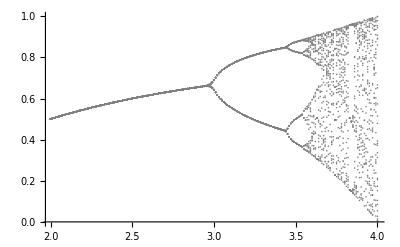

```mathematica
Clear[r,x];x0=0.1;
ziskejAtraktor[r_]:=(
dataL=RecurrenceTable[{x[n5] == r x[n5 - 1] (1 - x[n5 - 1]), x[0] == x0}, x, {n5, 0, 100}];
dataA=dataL[[-30;;Length[dataL]]];
Transpose[{Table[r,{i,1,Length[dataA]}],dataA}]
);
dataX=Table[ziskejAtraktor[r],{r,2,4,0.01}];
figX=ListPlot[Flatten[dataX,1],PlotStyle->Gray]
```

## Computation

```mathematica
tA[];
T1 =AbsoluteTiming[dat1=ParallelTable[{ii,BoxCount1[fceX[ii,EnD1]]},{ii,2.01,4,step}];][[1]]
tB[];
```

0.387742

TIME 00:00:00 30  #  Start 14:10:42 Friday 01/02 / Konec 14:10:42 Friday 01/02

```mathematica
tA[];
T11 =AbsoluteTiming[dat11=ParallelTable[{ii,BoxCount1[fceX[ii,EnD1]]},{ii,2.01,4,step}];][[1]]
tB[];

tA[];
T111=AbsoluteTiming[dat111=ParallelTable[{ii,BoxCount1[fceX[ii,EnD2]]},{ii,2.01,4,step}];][[1]]
tB[];
```

0.387457

TIME 00:00:00 30  #  Start 14:10:42 Friday 01/02 / Konec 14:10:42 Friday 01/02

3.48026

TIME 00:00:03 30  #  Start 14:10:42 Friday 01/02 / Konec 14:10:46 Friday 01/02

```mathematica
Show[{ListPlot[dat1,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}];
```

```mathematica
Show[{ListPlot[dat11,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}];
```

```mathematica
Show[{ListPlot[dat111,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}];
```

```mathematica
tA[];
T2=AbsoluteTiming[dat2=ParallelTable[{ii,corrDIMdim1[fceX[ii,EnD]]},{ii,2,4,step}];][[1]]
tB[];
```

1.24744

TIME 00:00:01 30  #  Start 14:10:46 Friday 01/02 / Konec 14:10:47 Friday 01/02

```mathematica
tA[];
T22=AbsoluteTiming[dat22=ParallelTable[{ii,corrDIMdim1[fceX[ii,EnD1]]},{ii,2,4,step}];][[1]]
tB[];
```

26.435

TIME 00:00:26 30  #  Start 14:10:47 Friday 01/02 / Konec 14:11:14 Friday 01/02

```mathematica
tA[];
T222=AbsoluteTiming[dat222=ParallelTable[{ii,corrDIMdim1[fceX[ii,EnD2]]},{ii,2,4,step}];][[1]]
tB[];
```

$Aborted

TIME 00:00:57 30  #  Start 14:11:14 Friday 01/02 / Konec 14:12:12 Friday 01/02

```mathematica
Show[{ListPlot[dat2,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}];
```

```mathematica
Show[{ListPlot[dat22,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}];
```

```mathematica
Show[{ListPlot[dat222,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}];
```

```mathematica
tA[];
T3 =AbsoluteTiming[dat3=ParallelTable[{ii,Lyapun2[fceX[ii,EnD]]},{ii,2.,4,step}];][[1]]
tB[];
```

3.32308

TIME 00:00:03 30  #  Start 14:09:14 Friday 01/02 / Konec 14:09:18 Friday 01/02

```mathematica
tA[];
T33=AbsoluteTiming[dat33=ParallelTable[{ii,Lyapun2[fceX[ii,EnD1]]},{ii,2.,4,step}];][[1]]
tB[];
```

3.16722

TIME 00:00:03 30  #  Start 14:09:18 Friday 01/02 / Konec 14:09:21 Friday 01/02

```mathematica
tA[];
T333=AbsoluteTiming[dat333=ParallelTable[{ii,Lyapun2[fceX[ii,EnD2]]},{ii,2.,4,step}];][[1]]
tB[];
```

3.28045

TIME 00:00:03 30  #  Start 14:09:21 Friday 01/02 / Konec 14:09:24 Friday 01/02

```mathematica
Show[{ListPlot[dat3,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{-3,1}}];
```

```mathematica
Show[{ListPlot[dat33,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{-3,1}}];
```

```mathematica
Show[{ListPlot[dat333,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{-3,1}}];
```

```mathematica
tA[];
T4 =AbsoluteTiming[dat4=ParallelTable[{ii,f1[fceX[ii,EnD]]},{ii,2.,4,step}];][[1]]
tB[];
```

0.0792046

TIME 00:00:00 30  #  Start 14:09:24 Friday 01/02 / Konec 14:09:25 Friday 01/02

```mathematica
tA[];
T44 =AbsoluteTiming[dat44=ParallelTable[{ii,f1[fceX[ii,EnD1]]},{ii,2.,4,step}];][[1]]
tB[];
```

0.0611989

TIME 00:00:00 30  #  Start 14:09:25 Friday 01/02 / Konec 14:09:25 Friday 01/02

```mathematica
tA[];
T444 =AbsoluteTiming[dat444=ParallelTable[{ii,f1[fceX[ii,EnD2]]},{ii,2.,4,step}];][[1]]
tB[];
```

0.0755597

TIME 00:00:00 30  #  Start 14:09:25 Friday 01/02 / Konec 14:09:25 Friday 01/02

```mathematica
Show[{ListPlot[Table[Flatten[dat4[[i]]],{i,1,Length[dat4]}],PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}];
```

```mathematica
Show[{ListPlot[Table[Flatten[dat44[[i]]],{i,1,Length[dat4]}],PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}];
```

```mathematica
Show[{ListPlot[Table[Flatten[dat444[[i]]],{i,1,Length[dat4]}],PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}];
```

```mathematica
tA[];
T5 =AbsoluteTiming[dat5=ParallelTable[{ii,Rp1[fceX[ii,EnD]]},{ii,2.,4,step}];][[1]]
tB[];
```

0.191518

TIME 00:00:00 30  #  Start 14:09:25 Friday 01/02 / Konec 14:09:25 Friday 01/02

```mathematica
tA[];
T55 =AbsoluteTiming[dat55=ParallelTable[{ii,Rp1[fceX[ii,EnD1]]},{ii,2.,4,step}];][[1]]
tB[];
```

0.166294

TIME 00:00:00 30  #  Start 14:09:25 Friday 01/02 / Konec 14:09:25 Friday 01/02

```mathematica
tA[];
T555=AbsoluteTiming[dat555=ParallelTable[{ii,Rp1[fceX[ii,EnD2]]},{ii,2.,4,step}];][[1]]
tB[];
```

0.165048

TIME 00:00:00 30  #  Start 14:09:25 Friday 01/02 / Konec 14:09:26 Friday 01/02

```mathematica
Show[{ListPlot[dat5B = Table[{dat5[[i]][[1]],dat5[[i]][[2]][[2]]},{i,1,Length[dat4]}],PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}];
```

```mathematica
Show[{ListPlot[dat55B =Table[{dat55[[i]][[1]],dat55[[i]][[2]][[2]]},{i,1,Length[dat44]}],PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}];
```

```mathematica
Show[{ListPlot[dat555B =Table[{dat555[[i]][[1]],dat555[[i]][[2]][[2]]},{i,1,Length[dat444]}],PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}];
```

```mathematica
tA[];
T6 =AbsoluteTiming[dat6=ParallelTable[{ii,RpAl[fceX[ii,EnD]]},{ii,2.,4,step}];][[1]]
tB[];
```

0.185323

TIME 00:00:00 30  #  Start 14:09:26 Friday 01/02 / Konec 14:09:26 Friday 01/02

```mathematica
tA[];
T66=AbsoluteTiming[dat66=ParallelTable[{ii,RpAl[fceX[ii,EnD1]]},{ii,2.,4,step}];][[1]]
tB[];
```

0.168535

TIME 00:00:00 30  #  Start 14:09:26 Friday 01/02 / Konec 14:09:26 Friday 01/02

```mathematica
tA[];
T666=AbsoluteTiming[dat666=ParallelTable[{ii,RpAl[fceX[ii,EnD2]]},{ii,2.,4,step}];][[1]]
tB[];
```

0.166556

TIME 00:00:00 30  #  Start 14:09:26 Friday 01/02 / Konec 14:09:26 Friday 01/02

```mathematica
D63 =Table[{dat6[[i]][[1]],dat6[[i]][[2]][[3]]},{i,1,Length[dat4]}];

Show[{ListPlot[dat6C=Table[{dat6[[i]][[1]],dat6[[i]][[2]][[3]]/Max[D63]},{i,1,Length[dat4]}],PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]  ;(*normed*)
```

```mathematica
D64 =Table[{dat6[[i]][[1]],dat6[[i]][[2]][[4]]},{i,1,Length[dat4]}];

Show[{ListPlot[dat6D =Table[{dat6[[i]][[1]],dat6[[i]][[2]][[4]]/Max[D64]},{i,1,Length[dat4]}],PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}] ;(*normed*)
```

```mathematica
D663 =Table[{dat66[[i]][[1]],dat66[[i]][[2]][[3]]},{i,1,Length[dat44]}];

Show[{ListPlot[dat66C=Table[{dat66[[i]][[1]],dat66[[i]][[2]][[3]]/Max[D663]},{i,1,Length[dat44]}],PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}] ; (*normed*)
```

```mathematica
D664 =Table[{dat66[[i]][[1]],dat66[[i]][[2]][[4]]},{i,1,Length[dat44]}];

Show[{ListPlot[dat66D =Table[{dat66[[i]][[1]],dat66[[i]][[2]][[4]]/Max[D664]},{i,1,Length[dat44]}],PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}] ;(*normed*)
```

```mathematica
D6663 =Table[{dat666[[i]][[1]],dat666[[i]][[2]][[3]]},{i,1,Length[dat444]}];

Show[{ListPlot[dat666C =Table[{dat666[[i]][[1]],dat666[[i]][[2]][[3]]/Max[D6663]},{i,1,Length[dat444]}],PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]  ;(*normed*)
```

```mathematica
D6664 =Table[{dat666[[i]][[1]],dat666[[i]][[2]][[4]]},{i,1,Length[dat444]}];

Show[{ListPlot[dat666D = Table[{dat666[[i]][[1]],dat666[[i]][[2]][[4]]/Max[D6664]},{i,1,Length[dat444]}],PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}] ;(*normed*)
```

## Machine learning

```mathematica
TRA2[da_]:= Flatten[1-{da- Min[da]}/Max[{da- Min[da]}],1];
```

```mathematica
TRA1[da_]:= Flatten[{da- Min[da]}/Max[{da- Min[da]}],1];
```

```mathematica
dat444;
```

```mathematica
dat666D;
dat666C;
```

```mathematica
dat555B;
```

```mathematica
dat333;
```

```mathematica
dat222;
```

```mathematica
D1 = Take[Table[dat111[[i]][[2]],{i,1,Length[dat111]}],-200];D2= Take[Table[dat222[[i]][[2]],{i,1,Length[dat222]}],-200];D3 =Take[ Table[dat333[[i]][[2]],{i,1,Length[dat333]}],-200];D4=Take[ Table[dat444[[i]][[2]],{i,1,Length[dat444]}],-200];D5 =Take[ Table[dat555B[[i]][[2]],{i,1,Length[dat555]}],-200];D6 = Take[Table[dat666C[[i]][[2]],{i,1,Length[dat666]}],-200];D7 =Take[ Table[dat666D[[i]][[2]],{i,1,Length[dat777]}],-200];
```

```mathematica
TRST = TRA1[D1]+TRA1[D2] + TRA1[D3] + TRA2[D4] + TRA2[D5] + TRA2[D6] + TRA2[D7];
```

```mathematica
ListPlot[CH =TRST/ Max[TRST]];
```

```mathematica
LM=Take[ParallelTable[fceX[ii,EnD2],{ii,2.,4,0.01}],-200];


TTR1 = Table[LM [[i]] -> CH[[i]],{i,1,200}];
FIN  =RandomSample[TTR1,100];
```

```mathematica
p1 = Predict[FIN,Method->"DecisionTree"]; p2= Predict[FIN,Method->"NeuralNetwork"]; p3 = Predict[FIN,Method->"LinearRegression"]; p4 = Predict[FIN,Method->"RandomForest"]; p5 = Predict[FIN,Method->"GaussianProcess"]; p6 = Predict[FIN,Method->"NearestNeighbors"]; p7 = Predict[FIN,Method->"GradientBoostedTrees"];
```

```mathematica
tA[];
T777=AbsoluteTiming[dat777=ParallelTable[{ii,p1[fceX[ii,EnD2]]},{ii,2.01,4,step}];][[1]]
tB[];
```

0.273554

TIME 00:00:00 30  #  Start 14:09:43 Friday 01/02 / Konec 14:09:43 Friday 01/02

```mathematica
ListPlot[dat777];
```

```mathematica
tA[];
TM1=AbsoluteTiming[datm1=ParallelTable[{ii,p1[fceX[ii,EnD2]]},{ii,2,4,step}];][[1]]
tB[];
tA[];
TM2=AbsoluteTiming[datm2=ParallelTable[{ii,p2[fceX[ii,EnD2]]},{ii,2,4,step}];][[1]]
tB[];
tA[];
TM3=AbsoluteTiming[datm3=ParallelTable[{ii,p3[fceX[ii,EnD2]]},{ii,2,4,step}];][[1]]
tB[];
tA[];
TM4=AbsoluteTiming[datm4=ParallelTable[{ii,p4[fceX[ii,EnD2]]},{ii,2,4,step}];][[1]]
tB[];
tA[];
TM5=AbsoluteTiming[datm5=ParallelTable[{ii,p5[fceX[ii,EnD2]]},{ii,2,4,step}];][[1]]
tB[];
tA[];
TM6=AbsoluteTiming[datm6=ParallelTable[{ii,p6[fceX[ii,EnD2]]},{ii,2,4,step}];][[1]]
tB[];
tA[];
TM7=AbsoluteTiming[datm7=ParallelTable[{ii,p7[fceX[ii,EnD2]]},{ii,2,4,step}];][[1]]
tB[];
```

0.268519

TIME 00:00:00 30  #  Start 14:09:44 Friday 01/02 / Konec 14:09:44 Friday 01/02

2.82749

TIME 00:00:02 30  #  Start 14:09:44 Friday 01/02 / Konec 14:09:47 Friday 01/02

0.346862

TIME 00:00:00 30  #  Start 14:09:47 Friday 01/02 / Konec 14:09:47 Friday 01/02

0.582009

TIME 00:00:00 30  #  Start 14:09:47 Friday 01/02 / Konec 14:09:48 Friday 01/02

0.397557

TIME 00:00:00 30  #  Start 14:09:48 Friday 01/02 / Konec 14:09:48 Friday 01/02

0.306424

TIME 00:00:00 30  #  Start 14:09:48 Friday 01/02 / Konec 14:09:48 Friday 01/02

0.705323

TIME 00:00:00 30  #  Start 14:09:48 Friday 01/02 / Konec 14:09:49 Friday 01/02

## Plotting

```mathematica
pic11=Show[{figX,ListPlot[dat11,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Box-counting dimension"}];
```

```mathematica
pic111=Show[{figX,ListPlot[dat111,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Box-counting dimension D_0"}];
```

```mathematica
pic2=Show[{figX,ListPlot[dat2,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Correlation dimension"}];
```

```mathematica
pic22=Show[{figX,ListPlot[dat22,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Correlation dimension"}];
```

```mathematica
pic222=Show[{figX,ListPlot[dat222,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Correlation dimension D_2"}];
```

```mathematica
pic3=Show[{figX,ListPlot[dat3,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{-3,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Lyapunov exponent from time series λ_m"}];
```

```mathematica
pic33=Show[{figX,ListPlot[dat33,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{-3,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Lyapunov exponent from time series"}];
```

```mathematica
pic333=Show[{figX,ListPlot[dat333,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{-3,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Lyapunov exp. from time series λ"}];
```

```mathematica
pic4=Show[{figX,ListPlot[dat4,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","RQA - RR"}];
```

```mathematica
pic44=Show[{figX,ListPlot[dat44,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","RQA - RR"}];
```

```mathematica
pic444=Show[{figX,ListPlot[dat444,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","RQA - RR"}];
```

```mathematica
pic5=Show[{figX,ListPlot[dat5B,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","RQA - DET"}];
```

```mathematica
pic55=Show[{figX,ListPlot[dat55B,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","RQA - DET"}];
```

```mathematica
pic555=Show[{figX,ListPlot[dat555B,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","RQA - DET"}];
```

```mathematica
pic6=Show[{figX,ListPlot[dat6C,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","RQA - ENTR"}];
```

```mathematica
pic66=Show[{figX,ListPlot[dat66C,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","RQA - ENTR"}];
```

```mathematica
pic666=Show[{figX,ListPlot[dat666C,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","RQA - ENTR"}];
```

```mathematica
pic7=Show[{figX,ListPlot[dat6D,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","RQA - LL"}];
```

```mathematica
pic77=Show[{figX,ListPlot[dat66D,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","RQA - LL"}];
```

```mathematica
pic777=Show[{figX,ListPlot[dat666D,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","RQA - LL"}];
```

```mathematica
pic8=Show[{figX,ListPlot[dat7,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Machine learning"}];
```

```mathematica
pic88=Show[{figX,ListPlot[dat77,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Machine learning"}];
```

```mathematica
pic888=Show[{figX,ListPlot[dat777,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Machine learning"}];
```

```mathematica
picm1=Show[{figX,ListPlot[datm1,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","ML  Decision Tree"}];
```

```mathematica
picm2=Show[{figX,ListPlot[datm2,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","ML  Neural Network"}];
```

```mathematica
picm3=Show[{figX,ListPlot[datm3,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","ML  Linear Regression"}];
```

```mathematica
picm4=Show[{figX,ListPlot[datm4,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","ML  Random Forest"}];
```

```mathematica
picm5=Show[{figX,ListPlot[datm5,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","ML  Gaussian Process"}];
```

```mathematica
picm6=Show[{figX,ListPlot[datm6,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","ML  Nearest Neighbors"}];
```

```mathematica
picm7=Show[{figX,ListPlot[datm7,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","ML  Gradient Boosted Trees"}];
```

```mathematica
FinalPic=GraphicsGrid[{{pic111,pic222,pic444,pic555},{pic666,pic777,pic333,picL},{picm1,picm2,picm3,picm4},{picm5,picm6,picm7}}]
```

```mathematica
Export["FinalPic.pdf",FinalPic];
```